```mathematica
AS0 = 10^-49;
IS0 = 9*10^-46;
VS0 = 3.24*10^-46;

Af0 = 215;
If0 = 150;
Vf0 = 500;

Afs = 20;
Ifs = 40;
Vfs = 20;
x[f_]:=f/f0;
ASh[f_]:=Piecewise[{{S0*(x[f]^-4.14-5 x[f]^-2+111(1-x[f]^2+x[f]^4/2)/(1+x[f]^2/2)), f>=fs}, {Infinity, f <fs}}] /. {S0->AS0, f0->Af0, fs->Afs};

ISh[f_]:=Piecewise[{{S0*((4.49x[f])^-56+0.16 x[f]^-4.52+0.52+0.32 x[f]^2), f>=fs}, {Infinity, f <fs}}] /. {S0->IS0, f0->If0, fs->Ifs};

VSh[f_]:=Piecewise[{{S0*((6.23x[f])^-5+2 x[f]^-1+1+x[f]^2), f>=fs}, {Infinity, f <fs}}] /. {S0->VS0,f0->Vf0,fs->Vfs};
```

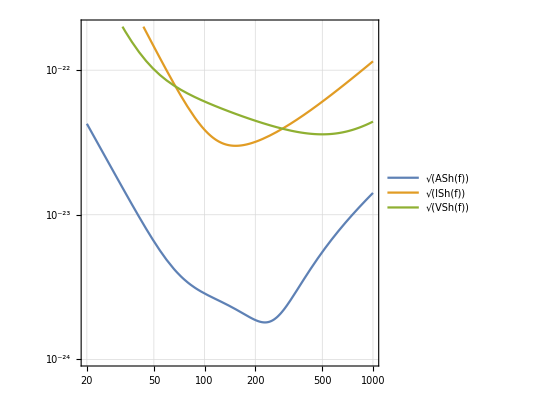

```mathematica
LogLogPlot[{Sqrt[ASh[f]], Sqrt[ISh[f]], Sqrt[VSh[f]]},{f, 10, 10^3}, PlotTheme -> "Detailed", PlotRange -> {{2 10, 10^3}, {10^-24,0.2*10^-21}}, AspectRatio->1]
```

```mathematica
(* Distance for fixed SNR *)
rho0 = 5;
eta[m1_, m2_]:=(m1*m2)/(m1+m2)^2;
G =6.67*10^-11;
c = 299792458;
Mpc = 10^6*3.26*9.46*10^15;
Mdot = 1.989*10^30;

flso[M_] := (6^(3/2)*Pi*G/c^3*M)^-1;

Dist[M_,eta_, Sh_, fs_]:=1/(rho0 * Pi^(2/3))Sqrt[(2 * eta* (G*M)^(5/3))/(15*c^3)](NIntegrate[f^(-7/3)/Sh[f], {f, fs, flso[M]}])^(1/2);
```

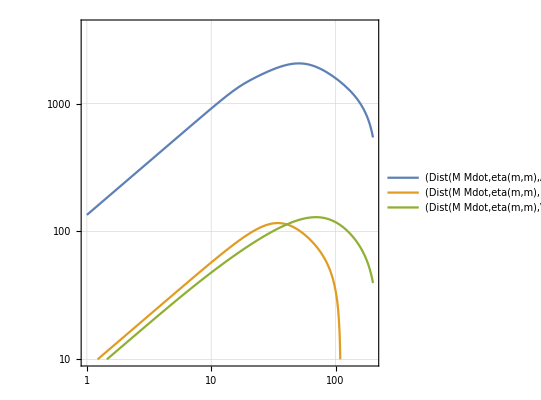

```mathematica
LogLogPlot[{Dist[M*Mdot,eta[m, m], ASh, Afs]/Mpc, Dist[M*Mdot,eta[m, m], ISh, Ifs]/Mpc, Dist[M*Mdot,eta[m, m], VSh, Vfs]/Mpc}, {M, 1, 200}, PlotTheme -> "Detailed", PlotRange->{10, 4*10^3}, AspectRatio->1]
```

```mathematica
(* Signal parameters *)

Mdot = 1.989*10^30;

(*
m1 =1.4*Mdot; 
m2 = 1.4*Mdot; 
M[m1_, m2_]:= m1 + m2;
eta[m1_, m2_]:=(m1 * m2)/M[m1, m2]^2;
Mch[m1_, m2_] := eta[m1, m2]^(3/5)M[m1, m2]; 
*)
v [f_, M_]:=(Pi * M*f)^(1/3);
flso[M_] := (6^(3/2)*Pi*G/c^3*M)^-1;

theta = -11831/9240;
lambda = -1987/3080;

f1[eta_,f_,M_]:=1;
f2[eta_,f_,M_]:=0;
f3[eta_, f_, M_]:=20/9(743/336+11/4 eta);
f4[eta_, f_, M_]:=-16Pi;
f5[eta_, f_, M_]:=10(3058673/1016064+5429/1008 eta+617/144 eta^2);
f6[eta_, f_, M_]:=Pi(38645/756+38645/252 Log[v[f, M]/v[flso[M], M]]-65/9 eta(1 + 3Log[v[f, M]/v[flso[M], M]]));
f7[eta_,f_, M_]:=(11583231236531/4694215680-(640*Pi^2)/3-(6848*EulerGamma)/21)+eta(-15335597827/3048192+(2255 Pi^2)/12-(1760*theta)/3+(12320*lambda)/9)+76055/1728 eta^2-127825/1296 eta^3-6848/21 Log[4*v[f, M]];
f8[eta_, f_, M_]:=Pi(77096675/254016+378515/1512 eta-74045/756 eta^2);

a=Range[8];
a[[1]]=f1;
a[[2]]=f2;
a[[3]]=f3;
a[[4]]=f4;
a[[5]]=f5;
a[[6]]=f6;
a[[7]]=f7;
a[[8]]=f8;
```

```mathematica
psi[f_, tc_, phic_, M_, eta_]:=2*Pi*f *tc-phic-Pi/4+3/(128*eta*v[f, M]^5)Sum[a[[k+1]][eta, f, M] v[f, M]^k, {k, 0, 7}];
h[f_, A_, tc_, phic_, M_, eta_ ]:=A*f^(-7/6)*Exp[I*psi[f, tc, phic, eta, M]]/.{A->Exp[A], tc->tc/f0, M->Exp[M]/eta^(3/5)} /.{eta->Exp[eta]};
```

```mathematica
nwip[g_, h_, Sh_, M_]:=2 * Integrate[(Simplify[Conjugate[g[f]] * h[f] + g[f] * Conjugate[h[f]], Assumptions-> f∈Reals && f>0])/Sh[f], {f, 0, flso[M]}];
```

```mathematica
(* Fisher matrix *)
m1=1.4*Mdot;
m2=1.4*Mdot;

Mreal = m1 + m2;
etareal = (m1*m2)/Mreal^2;
Mchreal=etareal^(3/5)Mreal;
logetareal = Log[etareal];
logMchreal = Log[Mchreal];

Q=Sqrt[5/24];
Distreal=Dist[Mreal, etareal, ASh, Afs];
Areal=Q*Mchreal^(5/6)/Distreal;
logAreal=Log[Areal];

(*
A -> 1,
tc -> 2,
phic -> 3,
M -> 4,
eta -> 5
*)
h1[f_]:=D[h[f, A, tc, phic, M, eta] , A]  /. {f0 -> Af0, A->logAreal, tc->0, phic->0, M->logMchreal, eta->logetareal};
h2[f_]:=D[h[f, A, tc, phic, M, eta] , tc]  /. {f0 -> Af0, A->logAreal, tc->0, phic->0, M->logMchreal, eta->logetareal};
h3[f_]:=D[h[f, A, tc, phic, M, eta] , phic]  /. {f0 -> Af0, A->logAreal, tc->0, phic->0, M->logMchreal, eta->logetareal};
h4[f_]:=D[h[f, A, tc, phic, M, eta] , M]  /. {f0 -> Af0, A->logAreal, tc->0, phic->0, M->logMchreal, eta->logetareal};
h5[f_]:=D[h[f, A, tc, phic, M, eta] , eta]  /. {f0 -> Af0, A->logAreal, tc->0, phic->0, M->logMchreal, eta->logetareal};

partials={h1, h2, h3, h4, h5};

FisherMatrix=Table[nwip[partials[[i]], partials[[j]], ASh, Mreal], {i, 1, 5}, {j, 1, 5}]
CorrelationMatrix=Inverse[FisherMatrix]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{1.76579×10^45,0.+0. ⅈ,0.,0.591439-0.785785 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,3.99882×10^46,-7.09829×10^45-6.30862×10^31 ⅈ,-5.23542×10^108-4.63582×10^94 ⅈ,2.26868×10^108},{0.,-7.09829×10^45-6.30862×10^31 ⅈ,1.76579×10^45,1.15843×10^108,-5.01985×10^107-4.37464×10^93 ⅈ},{0.591439-0.785785 ⅈ,-5.23542×10^108-4.63582×10^94 ⅈ,1.15843×10^108,7.9161×10^170,0.+0. ⅈ},{0.+0. ⅈ,2.26868×10^108,-5.01985×10^107-4.37464×10^93 ⅈ,0.+0. ⅈ,1.48647×10^170}}

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.76579×10^45+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.591439-0.785785 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,3.99882×10^46+0. ⅈ,-7.09829×10^45-6.30862×10^31 ⅈ,-5.23542×10^108-4.63582×10^94 ⅈ,2.26868×10^108+0. ⅈ},«1»,{0.591439-0.785785 ⅈ,-5.23542×10^108-4.63582×10^94 ⅈ,«1»,«23»+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,2.26868×10^108+0. ⅈ,-5.01985×10^107-4.37464×10^93 ⅈ,0.+0. ⅈ,1.48647×10^170+0. ⅈ}} may contain significant numerical errors.

{{5.66319×10^-46+1.43484×10^-264 ⅈ,2.15118×10^-155-2.85805×10^-155 ⅈ,-1.92866×10^-154+2.56241×10^-154 ⅈ,1.52125×10^-219-2.26269×10^-219 ⅈ,-9.79103×10^-217+1.30028×10^-216 ⅈ},{2.13189×10^-155-2.89918×10^-155 ⅈ,8.07838×10^-47+6.18172×10^-60 ⅈ,4.09446×10^-46+0. ⅈ,-6.4607×10^-110+7.20748×10^-112 ⅈ,1.48862×10^-109+1.66327×10^-111 ⅈ},{-1.91993×10^-154+2.56055×10^-154 ⅈ,4.08942×10^-46+2.38168×10^-49 ⅈ,1.45735×10^-45-2.13531×10^-48 ⅈ,5.74607×10^-109-1.05176×10^-111 ⅈ,-1.3223×10^-108-1.33061×10^-110 ⅈ},{1.3711×10^-219-1.82164×10^-219 ⅈ,-6.42252×10^-110+4.81906×10^-123 ⅈ,5.75817×10^-109+4.25247×10^-122 ⅈ,-4.09353×10^-174-2.77501×10^-185 ⅈ,2.92423×10^-171+0. ⅈ},{-9.79973×10^-217+1.30199×10^-216 ⅈ,1.48212×10^-109+1.18414×10^-122 ⅈ,-1.32881×10^-108+0. ⅈ,2.92579×10^-171+8.055×10^-185 ⅈ,-1.81943×10^-173+0. ⅈ}}

```mathematica
Clear["Global`*"]
```